```mathematica
hbar=1.054571817*10^-34;
bohr=5.29177210903*10^-11;
amu=1.66053892*10^-27;
coeff=(15*(250 bohr)*hbar^2*8 π^3*(6.53*100*140)/(133 amu)^2)^(1/5)*1000*√(3/4)/√2;
coeff*(30000)^(1/5)
```

1.21527

0.00198453

```mathematica
coeff=0.8*30000^(-1/5)
```

0.101781

```mathematica
d=coeff*(1/5)*30000^(-4/5)
```

5.33333×10^-6

```mathematica
d*3000
```

0.016

```mathematica
d*3000/0.8
```

0.02

```mathematica
tf=Max[1-(x^2/wx^2)-(y^2/wy^2)-(z^2/wz^2),0];
tfy=Integrate[tf,{y,-Infinity,Infinity},Assumptions->{wx>0,wy>0,wz>0,z>0,x>0,wx>x,√((wz^2 (wx^2-x^2))/wx^2)-z>0}]
```

(4 (wx^2 wy wz^2 √(1-x^2/wx^2-z^2/wz^2)-wy wz^2 x^2 √(1-x^2/wx^2-z^2/wz^2)-wx^2 wy z^2 √(1-x^2/wx^2-z^2/wz^2)))/(3 wx^2 wz^2)

```mathematica
tfyz=Integrate[Max[tfy,0],{z,-Infinity,Infinity},Assumptions->{wx>0,x>0,wx>x,wy>0,wz>0}]
```

(π wy wz (wx^2-x^2)^2)/(2 wx^4)

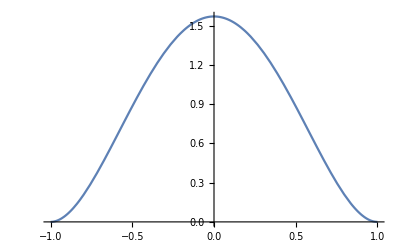

```mathematica
Plot[Max[tfyz,0]/.{wx->1,wy->1,wz->1},{x,-1,1}]
```

```mathematica
Solve[(1-x^2)^2==p,x]
```

{{x→-√(1-√p)},{x→√(1-√p)},{x→-√(1+√p)},{x→√(1+√p)}}

```mathematica
√(1-√0.9)
```

0.226532

```mathematica
form=√(1-√p);
D[form,p]
```

-1/(4 √(1-√p) √p)

```mathematica
(1-(0.2265)^2)
```

0.948698

```mathematica
N[Sqrt[5^2+6^2]]
```

7.81025